```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/berni/Dropbox/Projects/RapidiX/RapidiX

## Combine Results For Distributions

```mathematica
LOSet={1,5,9,13,17,21};
NLOSet=Join[LOSet,{2,6,10,14,18,22}];
NNLOSet=Join[NLOSet,{3,7,11,15,19,23}];
N3LOSet=Join[NNLOSet,{4,8,12,16,20,24}];
```

```mathematica
GetDistribution[file_,scale_,order_]:=
Block[{dist,max},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
dist=Table[
{N[i/10],Total[ToExpression[StringReplace[Import["../RapidiXLinux/Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
```

```mathematica
Export["Results/Rapidity_LO_mu125.m",GetDistribution[NNLO,125,LO]]
Export["Results/Rapidity_NLO_mu125.m",GetDistribution[NNLO,125,NLO]]
Export["Results/Rapidity_NNLO_mu125.m",GetDistribution[NNLO,125,NNLO]]

Export["Results/Rapidity_LO_mu31.25.m",GetDistribution[NNLO,31.25,LO]]
Export["Results/Rapidity_NLO_mu31.25.m",GetDistribution[NNLO,31.25,NLO]]
Export["Results/Rapidity_NNLO_mu31.25.m",GetDistribution[NNLO,31.25,NNLO]]

Export["Results/Rapidity_LO_mu62.5.m",GetDistribution[NNLO,62.5,LO]]
Export["Results/Rapidity_NLO_mu62.5.m",GetDistribution[NNLO,62.5,NLO]]
Export["Results/Rapidity_NNLO_mu62.5.m",GetDistribution[NNLO,62.5,NNLO]]
```

Results/Rapidity_LO_mu125.m

Results/Rapidity_NLO_mu125.m

Results/Rapidity_NNLO_mu125.m

Results/Rapidity_LO_mu31.25.m

Results/Rapidity_NLO_mu31.25.m

Results/Rapidity_NNLO_mu31.25.m

Results/Rapidity_LO_mu62.5.m

Results/Rapidity_NLO_mu62.5.m

Results/Rapidity_NNLO_mu62.5.m

```mathematica
GetExpDistribution[file_,scale_,order_,zbpow_]:=
Block[{dist,max},
If[MatchQ[order,LO],max=LOSet];
If[MatchQ[order,NLO],max=NLOSet];
If[MatchQ[order,NNLO],max=NNLOSet];
If[MatchQ[order,N3LO],max=N3LOSet];
dist=Table[
{N[i/10],Total[ToExpression[StringReplace[Import["../RapidiXLinux/Results/Rapidity/Rapidity_"<>ToString[file]<>"_Y"<>StringReplace[ToString[ToString[N[i/10]]]<>"_mu"<>ToString[scale]<>"_zbpow"<>ToString[zbpow]<>".txt",{"._"->"_"}]],{",}"->"}","e-"->"*10^-"}]][[max,1]]]},{i,0,44}];
dist=Join[{-#[[1]],#[[2]]}&/@Reverse[dist],dist]//DeleteDuplicates;
Return[dist];
];
```

```mathematica
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb0.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,0]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb1.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,1]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb2.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,2]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb3.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,3]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb4.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,4]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb5.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,5]]
Export["Results/Rapidity_NNLO_mu62.5_Unmatched_zb6.m",GetExpDistribution[NNLOUnmatched,62.5,NNLO,6]]
```

Results/Rapidity_NNLO_mu62.5_Unmatched_zb0.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb1.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb2.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb3.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb4.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb5.m

Results/Rapidity_NNLO_mu62.5_Unmatched_zb6.m

```mathematica
Export["Results/Rapidity_NNLO_mu62.5_NoRegular_zb0.m",GetExpDistribution[NNLONoRegular,62.5,NNLO,0]]
Export["Results/Rapidity_NNLO_mu62.5_NoRegular_zb1.m",GetExpDistribution[NNLONoRegular,62.5,NNLO,1]]
Export["Results/Rapidity_NNLO_mu62.5_NoRegular_zb2.m",GetExpDistribution[NNLONoRegular,62.5,NNLO,2]]
Export["Results/Rapidity_NNLO_mu62.5_NoRegular_zb3.m",GetExpDistribution[NNLONoRegular,62.5,NNLO,3]]
Export["Results/Rapidity_NNLO_mu62.5_NoRegular_zb4.m",GetExpDistribution[NNLONoRegular,62.5,NNLO,4]]
Export["Results/Rapidity_NNLO_mu62.5_NoRegular_zb5.m",GetExpDistribution[NNLONoRegular,62.5,NNLO,5]]
```

Results/Rapidity_NNLO_mu62.5_NoRegular_zb0.m

Results/Rapidity_NNLO_mu62.5_NoRegular_zb1.m

Results/Rapidity_NNLO_mu62.5_NoRegular_zb2.m

Results/Rapidity_NNLO_mu62.5_NoRegular_zb3.m

Results/Rapidity_NNLO_mu62.5_NoRegular_zb4.m

Results/Rapidity_NNLO_mu62.5_NoRegular_zb5.m

## NNLO Rapidity

```mathematica
LOCent=Get["Results/Rapidity_LO_mu62.5.m"];
NLOCent=Get["Results/Rapidity_NLO_mu62.5.m"];
NNLOCent=Get["Results/Rapidity_NNLO_mu62.5.m"];

LOMax=Get["Results/Rapidity_LO_mu125.m"];
NLOMax=Get["Results/Rapidity_NLO_mu125.m"];
NNLOMax=Get["Results/Rapidity_NNLO_mu125.m"];

LOMin=Get["Results/Rapidity_LO_mu31.25.m"];
NLOMin=Get["Results/Rapidity_NLO_mu31.25.m"];
NNLOMin=Get["Results/Rapidity_NNLO_mu31.25.m"];
```

```mathematica
dists={LOCent,NLOCent,NNLOCent,LOMax,LOMin,NLOMax,NLOMin,NNLOMax,NNLOMin};
```

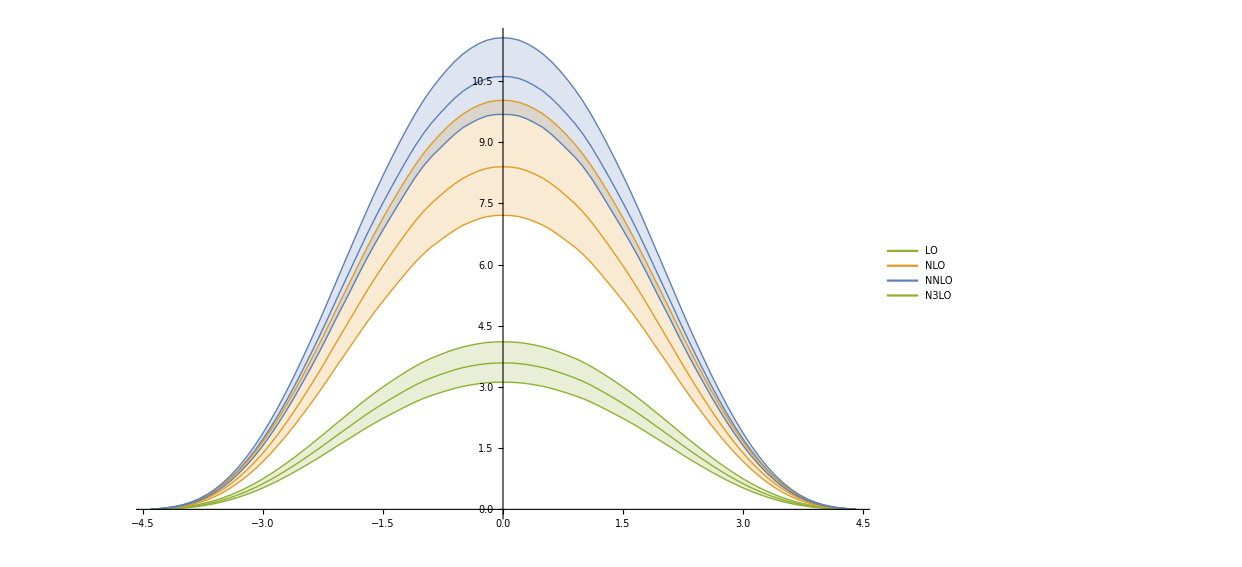

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[3]],Thick},
{ColorData[97,"ColorList"][[2]],Thick},
{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[3]],Thin},
{ColorData[97,"ColorList"][[3]],Thin},
{ColorData[97,"ColorList"][[2]],Thin},
{ColorData[97,"ColorList"][[2]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[4]],Thin},
{ColorData[97,"ColorList"][[4]],Thin}
},
Filling->{4->{1},5->{1},6->{2},7->{2},8->{3},9->{3},10->{4},11->{4}},
PlotLegends->Placed[LineLegend[{"LO\t     ","NLO\t","NNLO\t","N3LO\t"},LegendLayout->{"Row",3},LabelStyle->25],{0.85,0.8}]
]
```

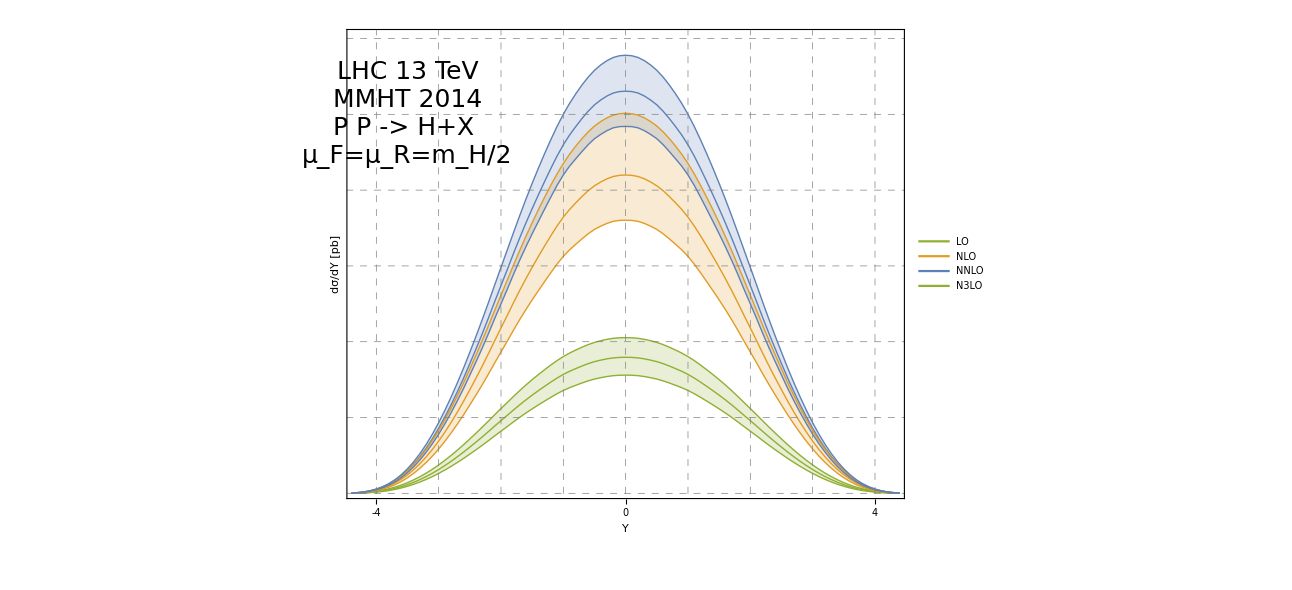

```mathematica
ppp=Show[pp,
PlotRange->{{-4.3,4.3},{0.1,12}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],2Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[2i,{i,-10,12}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ/dY [pb]"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",25,TextAlignment->Left],{-3.5,10}]
]
```

## NNLO Rapidity Approx -No Matching

```mathematica
NNLOCent=Get["Results/Rapidity_NNLO_mu62.5.m"];
NNLOMax=Get["Results/Rapidity_NNLO_mu125.m"];
NNLOMin=Get["Results/Rapidity_NNLO_mu31.25.m"];
```

```mathematica
Exp0=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb0.m"];
Exp1=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb1.m"];
Exp2=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb2.m"];
Exp3=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb3.m"];
Exp4=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb4.m"];
Exp5=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb5.m"];
Exp6=Get["Results/Rapidity_NNLO_mu62.5_Unmatched_zb6.m"];
```

```mathematica
NNLOCent
```

{{-4.4,0.00606535},{-4.3,0.0165244},{-4.2,0.0348639},{-4.1,0.0634312},{-4.,0.10501},{-3.9,0.162361},{-3.8,0.238197},{-3.7,0.335285},{-3.6,0.455564},{-3.5,0.600799},{-3.4,0.771716},{-3.3,0.968965},{-3.2,1.19199},{-3.1,1.44013},{-3.,1.71509},{-2.9,2.01505},{-2.8,2.33648},{-2.7,2.67962},{-2.6,3.04002},{-2.5,3.42255},{-2.4,3.81182},{-2.3,4.21396},{-2.2,4.63098},{-2.1,5.0608},{-2.,5.48173},{-1.9,5.90027},{-1.8,6.32585},{-1.7,6.73774},{-1.6,7.13245},{-1.5,7.511},{-1.4,7.8748},{-1.3,8.22872},{-1.2,8.57215},{-1.1,8.90018},{-1.,9.19481},{-0.9,9.45362},{-0.8,9.67771},{-0.7,9.88976},{-0.6,10.0842},{-0.5,10.2503},{-0.4,10.3772},{-0.3,10.4832},{-0.2,10.5614},{-0.1,10.6005},{0.,10.61},{0.1,10.6005},{0.2,10.5614},{0.3,10.4832},{0.4,10.3772},{0.5,10.2503},{0.6,10.0842},{0.7,9.88976},{0.8,9.67771},{0.9,9.45362},{1.,9.19481},{1.1,8.90018},{1.2,8.57215},{1.3,8.22872},{1.4,7.8748},{1.5,7.511},{1.6,7.13245},{1.7,6.73774},{1.8,6.32585},{1.9,5.90027},{2.,5.48173},{2.1,5.0608},{2.2,4.63098},{2.3,4.21396},{2.4,3.81182},{2.5,3.42255},{2.6,3.04002},{2.7,2.67962},{2.8,2.33648},{2.9,2.01505},{3.,1.71509},{3.1,1.44013},{3.2,1.19199},{3.3,0.968965},{3.4,0.771716},{3.5,0.600799},{3.6,0.455564},{3.7,0.335285},{3.8,0.238197},{3.9,0.162361},{4.,0.10501},{4.1,0.0634312},{4.2,0.0348639},{4.3,0.0165244},{4.4,0.00606535}}

```mathematica
dists={NNLOCent,NNLOMax,NNLOMin,Exp0,Exp1,Exp2,Exp3,Exp4,Exp5};
dists=Table[Table[{xrange[[j]],dists[[i,j,2]]/NNLOCent[[j,2]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

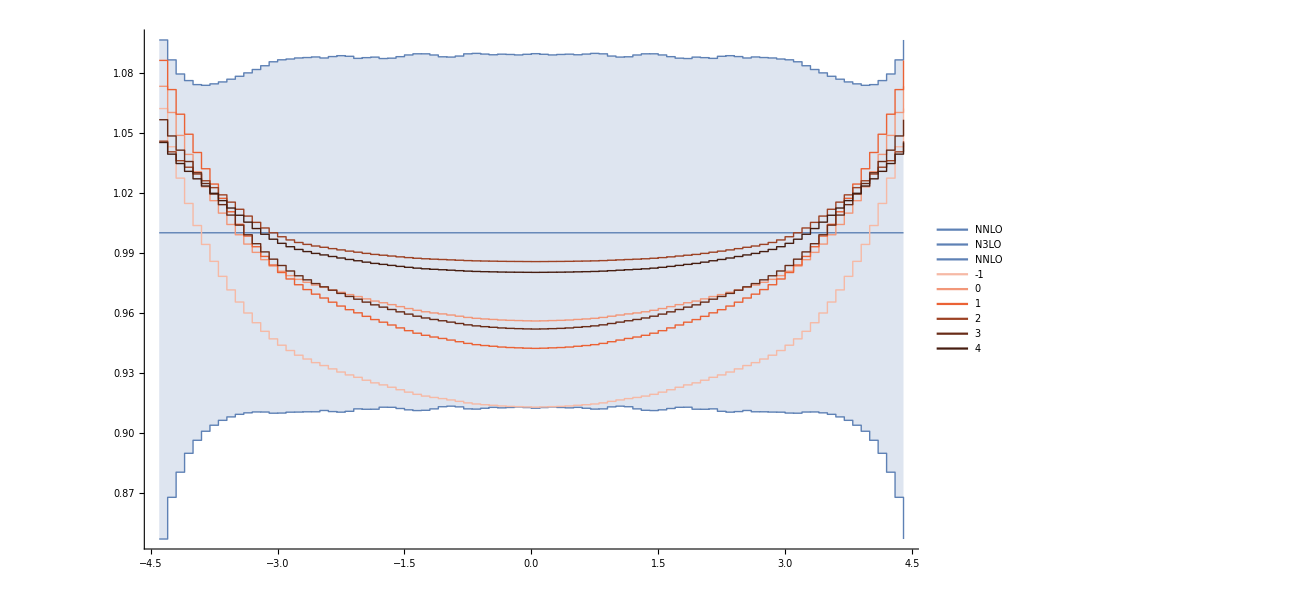

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[4]]//Lighter//Lighter,Thick},
{ColorData[97,"ColorList"][[4]]//Lighter,Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[4]]//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
Filling->{2->{1},3->{1}},
PlotLegends->Placed[LineLegend[{"NNLO\t","N3LO\t","NNLO",-1,0,1,2,3,4,5},LegendLayout->{"Row",3},LabelStyle->25],{0.85,0.2}],
PlotRange->All,InterpolationOrder->0
]
```

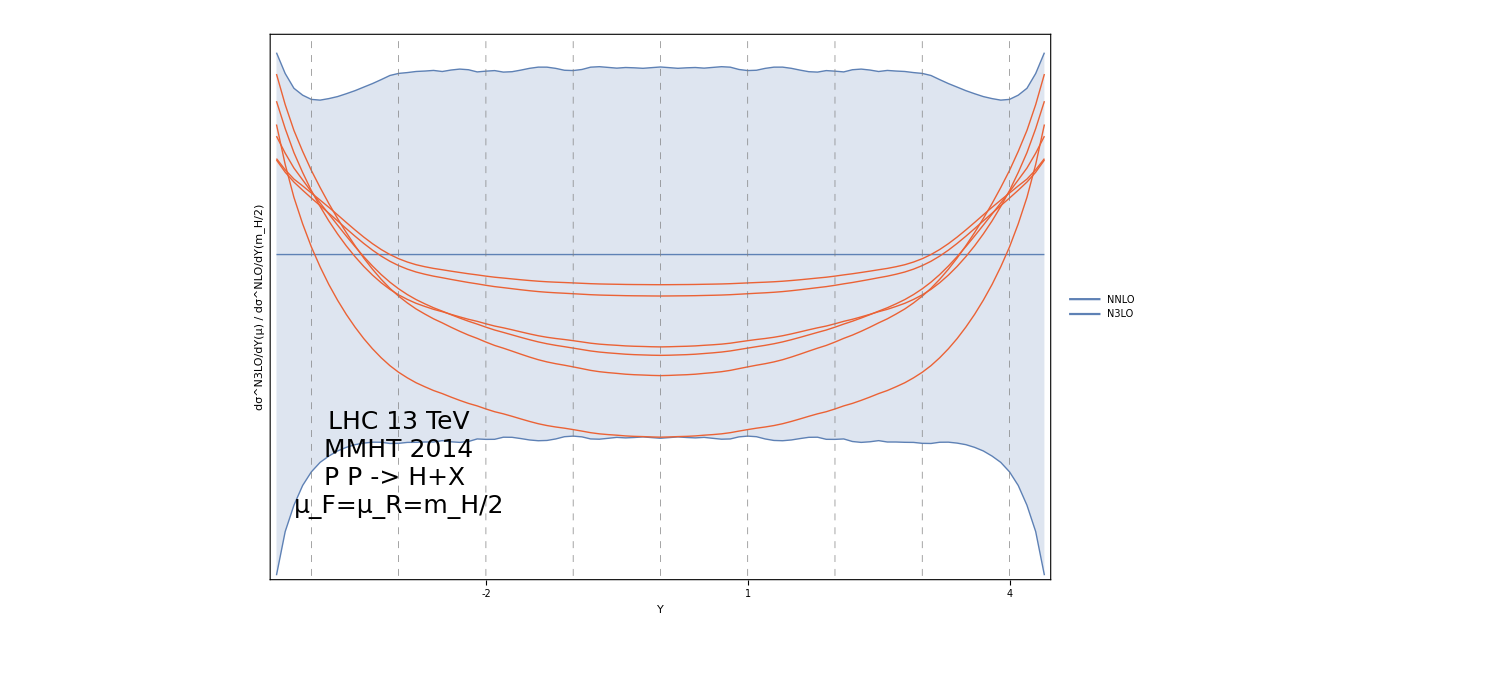

```mathematica
ppp=Show[pp,
PlotRange->{{-4.3,4.3},{0.85,1.1}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.05Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.05i,{i,-10,200}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ^N3LO/dY(μ) / dσ^NLO/dY(m_H/2)"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",25,TextAlignment->Left],{-3,0.9}]
]
```

## NNLO Rapidity Approx - No Regular

```mathematica
NNLOCent=Get["Results/Rapidity_NNLO_mu62.5.m"];
NNLOMax=Get["Results/Rapidity_NNLO_mu125.m"];
NNLOMin=Get["Results/Rapidity_NNLO_mu31.25.m"];
```

```mathematica
Exp0=Get["Results/Rapidity_NNLO_mu62.5_NoRegular_zb0.m"];
Exp1=Get["Results/Rapidity_NNLO_mu62.5_NoRegular_zb1.m"];
Exp2=Get["Results/Rapidity_NNLO_mu62.5_NoRegular_zb2.m"];
Exp3=Get["Results/Rapidity_NNLO_mu62.5_NoRegular_zb3.m"];
Exp4=Get["Results/Rapidity_NNLO_mu62.5_NoRegular_zb4.m"];
Exp5=Get["Results/Rapidity_NNLO_mu62.5_NoRegular_zb5.m"];
```

```mathematica
NNLOCent
```

{{-4.4,0.00606535},{-4.3,0.0165244},{-4.2,0.0348639},{-4.1,0.0634312},{-4.,0.10501},{-3.9,0.162361},{-3.8,0.238197},{-3.7,0.335285},{-3.6,0.455564},{-3.5,0.600799},{-3.4,0.771716},{-3.3,0.968965},{-3.2,1.19199},{-3.1,1.44013},{-3.,1.71509},{-2.9,2.01505},{-2.8,2.33648},{-2.7,2.67962},{-2.6,3.04002},{-2.5,3.42255},{-2.4,3.81182},{-2.3,4.21396},{-2.2,4.63098},{-2.1,5.0608},{-2.,5.48173},{-1.9,5.90027},{-1.8,6.32585},{-1.7,6.73774},{-1.6,7.13245},{-1.5,7.511},{-1.4,7.8748},{-1.3,8.22872},{-1.2,8.57215},{-1.1,8.90018},{-1.,9.19481},{-0.9,9.45362},{-0.8,9.67771},{-0.7,9.88976},{-0.6,10.0842},{-0.5,10.2503},{-0.4,10.3772},{-0.3,10.4832},{-0.2,10.5614},{-0.1,10.6005},{0.,10.61},{0.1,10.6005},{0.2,10.5614},{0.3,10.4832},{0.4,10.3772},{0.5,10.2503},{0.6,10.0842},{0.7,9.88976},{0.8,9.67771},{0.9,9.45362},{1.,9.19481},{1.1,8.90018},{1.2,8.57215},{1.3,8.22872},{1.4,7.8748},{1.5,7.511},{1.6,7.13245},{1.7,6.73774},{1.8,6.32585},{1.9,5.90027},{2.,5.48173},{2.1,5.0608},{2.2,4.63098},{2.3,4.21396},{2.4,3.81182},{2.5,3.42255},{2.6,3.04002},{2.7,2.67962},{2.8,2.33648},{2.9,2.01505},{3.,1.71509},{3.1,1.44013},{3.2,1.19199},{3.3,0.968965},{3.4,0.771716},{3.5,0.600799},{3.6,0.455564},{3.7,0.335285},{3.8,0.238197},{3.9,0.162361},{4.,0.10501},{4.1,0.0634312},{4.2,0.0348639},{4.3,0.0165244},{4.4,0.00606535}}

```mathematica
dists={NNLOCent,NNLOMax,NNLOMin,Exp0,Exp1,Exp2,Exp3,Exp4,Exp5};
dists=Table[Table[{xrange[[j]],dists[[i,j,2]]/NNLOCent[[j,2]]},{j,1,Length[dists[[i]]]}],{i,1,Length[dists]}];
```

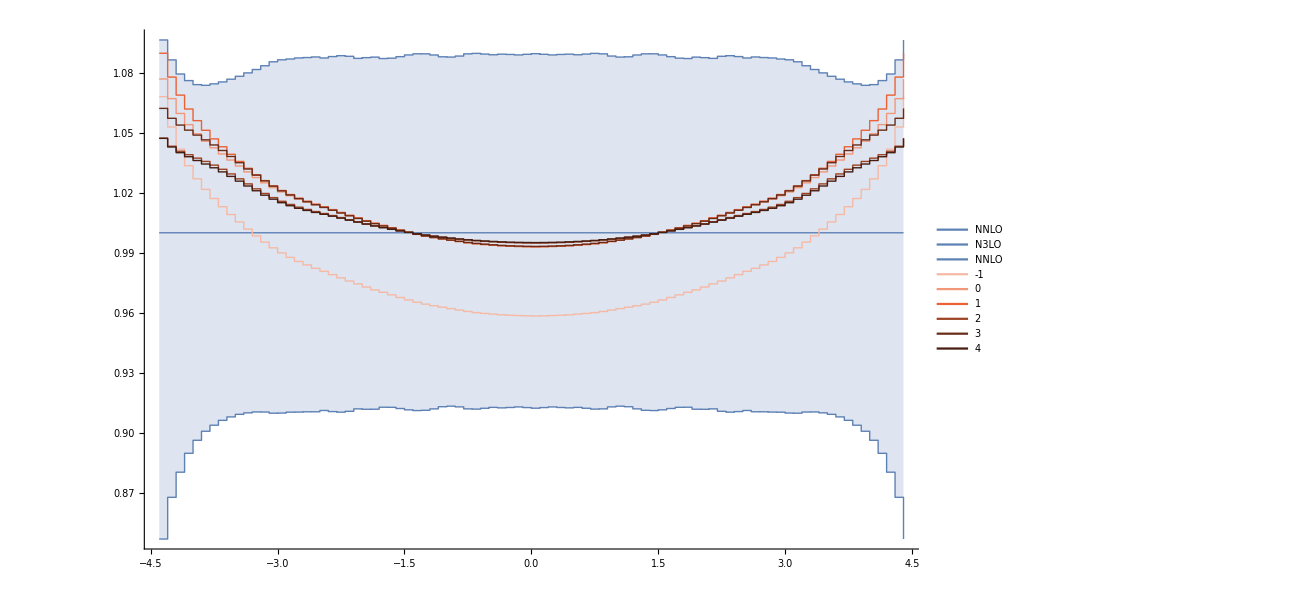

```mathematica
pp=ListLinePlot[dists
,PlotStyle->{{ColorData[97,"ColorList"][[1]],Thick},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[1]],Thin},
{ColorData[97,"ColorList"][[4]]//Lighter//Lighter,Thick},
{ColorData[97,"ColorList"][[4]]//Lighter,Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[4]]//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]]//Darker//Darker//Darker,Thick},
{ColorData[97,"ColorList"][[4]],Thick},
{ColorData[97,"ColorList"][[4]],Thick}
},
Filling->{2->{1},3->{1}},
PlotLegends->Placed[LineLegend[{"NNLO\t","N3LO\t","NNLO",-1,0,1,2,3,4,5},LegendLayout->{"Row",3},LabelStyle->25],{0.85,0.2}],
PlotRange->All,InterpolationOrder->0
]
```

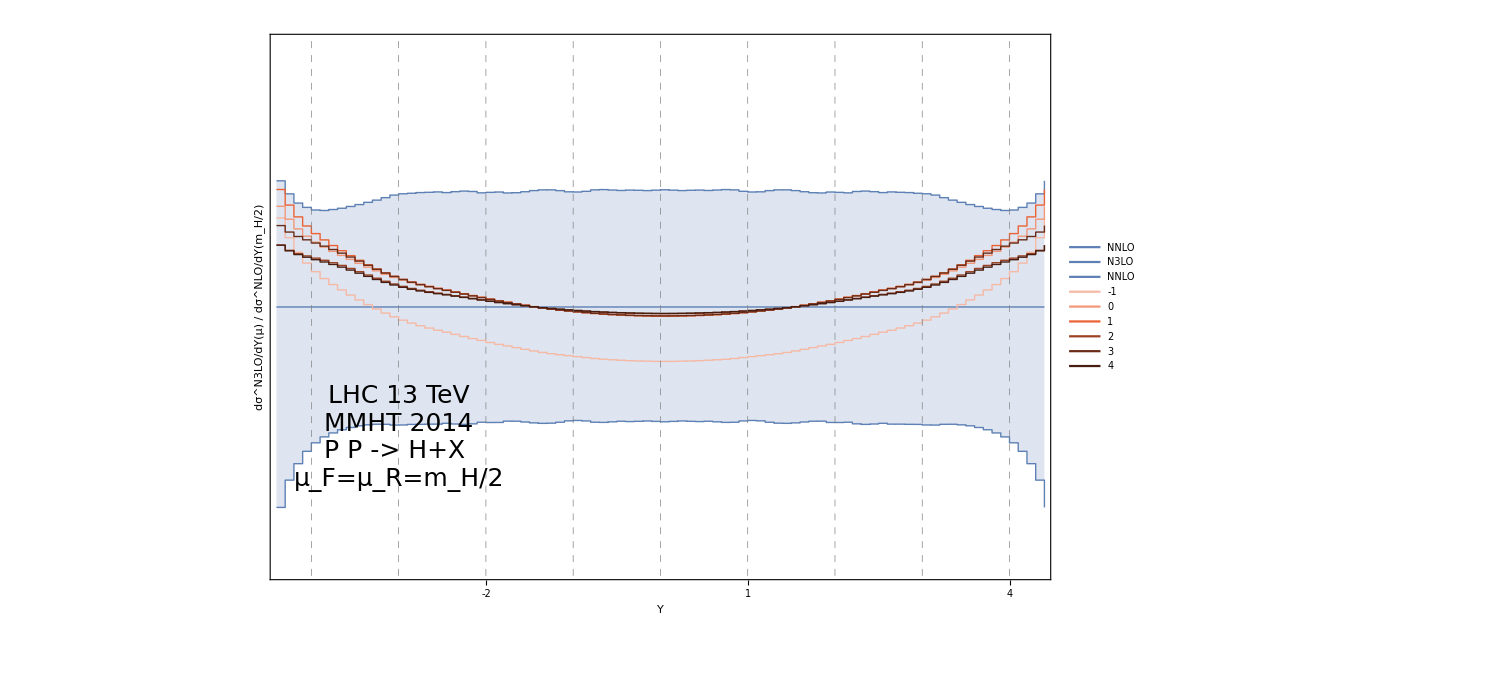

```mathematica
ppp=Show[pp,
PlotRange->{{-4.3,4.3},{0.8,1.2}},
Frame->True,
FrameTicks->{Table[{i,i} ,{i,-20,20}],0.05Table[{i,i},{i,-50,50}],None,None},
GridLines->{Table[i ,{i,-10,10}],Table[0.05i,{i,-10,200}]},
GridLinesStyle->Directive[Dashed,Thin,Gray],
AxesOrigin->{0,0},
FrameLabel->{" Y","dσ^N3LO/dY(μ) / dσ^NLO/dY(m_H/2)"},
LabelStyle->Directive[Bold,30],
Epilog->Inset[Style["LHC 13 TeV\nMMHT 2014\nP P -> H+X \nμ_F=μ_R=m_H/2",25,TextAlignment->Left],{-3,0.9}]
]
```